# Tools.wl Documentation

## Read Me!

** This version of JMSS Tools has add-ons and general reference material created by Alexi Rampono Kelly. Get the original at [https://github.com/frex-e/jmssTools] **

Please extract this file and the Tools.ws file (Move it out of the zip folder)

For the package to work, please run the following command in a Mathematica notebook within the same directory (same folder):

```mathematica
If[!ValueQ[Tools`isLoaded],SetDirectory[NotebookDirectory[]]; <<Tools.wl;"Tools.ws loaded","Tools.ws already loaded"]
```

Tools.ws loaded

Once this is done in any Mathematica notebook, all commands should work in all notebooks until you quit Mathematica.  
This notebook is set up to automatically run the initialisation script on startup.

To makes sure that the package has loaded correctly, run a command like the one below:

```mathematica
?TurningPointForm
```

Also, if the software malfunctions, resulting in you losing a mark, I’m honestly really sorry, but I’m not a professional programmer, I’m not even that good at it, I’m just doing this for fun in my free time, so use this at your own risk.

### Note if editing/contributing

This notebook is set so that it will not prompt you to save automatically to save me pain. (Though i will probably live to regret doing this).
If you wish to revert this, press control+shit+o and navigate to Notebook Options > File Options:
-Graphics-

Change the top drop down to Selected Notebook:
-Graphics-

Then tick the box next to ClosingSaveDialog:
-Graphics-

## General Mathematica Stuff

mostly by me, some stuff from Kermond xoxo

### Solve restrictions / assumptions

```mathematica
Solve[Integrate[Tan[x],{x,0,a}]==1,a]
```

{{a→ConditionalExpression[-ArcCos[1/ⅇ]+2 π C[1], C[1]∈ℤ&&C[1]≤0]},{a→ConditionalExpression[ArcCos[1/ⅇ]+2 π C[1], C[1]∈ℤ&&C[1]≤0]}}

This isn’t very helpful / abstract. We can add an assumption to limit the domain (works better than adding as a simultaneous condition)

```mathematica
Solve[Integrate[Tan[x],{x,0,a}]==1,a,Assumptions->-π/2<a<π/2]
```

{{a→-ArcCos[1/ⅇ]},{a→ArcCos[1/ⅇ]}}

Much Better :) - Other commands can accept assumptions too

```mathematica
FullSimplify[√(x^2)]
FullSimplify[√(x^2),Assumptions->x>0]
```

√(x^2)

x

### Getting the image of a transformed point

-Graphics-

```mathematica
QuickTransformMatrix[1/2,0,0,-2,x,y,-1/2,-2]
```

{{-1/2+x/2},{-2-2 y}}

```mathematica
Solve[0==-1/2+x/2,x]
Solve[0==-2-2 y,y]
```

{{x→1}}

{{y→-1}}

Therefor, (1, -1),

### Finding the rule of a function

-Graphics-

```mathematica
Clear[f]
f[x_]:=a/(x+b)+c
Solve[{f[1]==2,f[0]==5/3,1/f[3]==0},{a,b,c}]
```

{{a→-2,b→-3,c→1}}

```mathematica
f[x]/.{{a->-2,b->-3,c->1}}
```

{1-2/(-3+x)}

### Trig Function Period

until I add this to FunctionInfo[]

```mathematica
FunctionPeriod[Sin[Pi*x/7],x]
```

### Piecewise Function definitions

```mathematica
piece[x_]:=Piecewise[{{x^2+1,x<0},{x-1,x≥0}}]
piece[x]
```

Piecewise[{{1+x^2, x<0}, {-1+x, x≥0}, {0, True}}]

## Additional Commands

### DetailedPlot

Works the same as Plot, but adds intercepts, intersections, and stationary points.

Try mousing over the points!

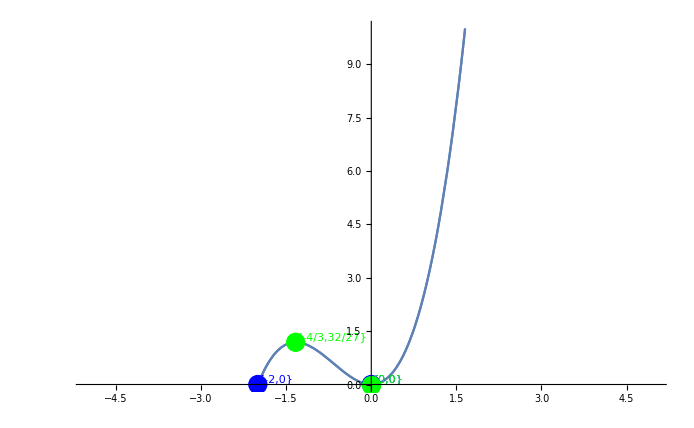

```mathematica
DetailedPlot[x^3+2 x^2,{x,-5,5},PlotRange->{0,10}]
```

Important: Leaving asymptotes can make the function quite slow. If in a rush, use Asymptotes -> False

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

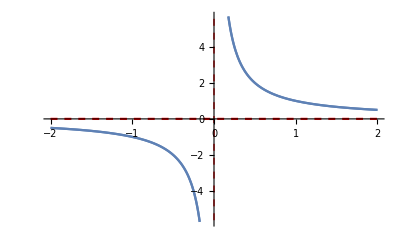

```mathematica
DetailedPlot[1/x,{x,-2,2}]
```

Types of points are colour coded:
Intersections: Red
Stationary Points: Green
Axes Intercepts: Blue
Closed Hole: Black
Open Hole: Gray

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

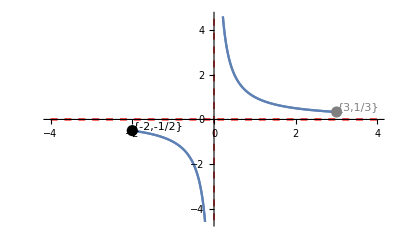

```mathematica
DetailedPlot[ConditionalExpression[1/x,-2<=x<3],{x,-4,4}]
```

In the case where 1 point may be 2 types, priority is Stationary Points > Intersections > Axes Intercepts

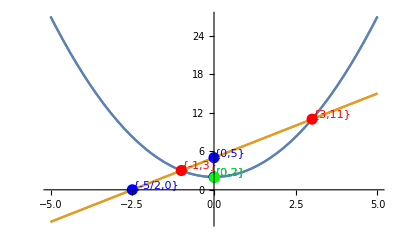

```mathematica
DetailedPlot[{x^2+2,2x+5},{x,-5,5}]
```

If you you wish to see labels in decimal form, DecimalPlaces → n, for n number of decimal places

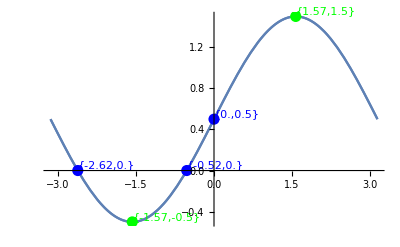

```mathematica
DetailedPlot[Sin[x]+1/2,{x,-π,π},DecimalPlaces->2]
```

As you can see, it can get a little cluttered:

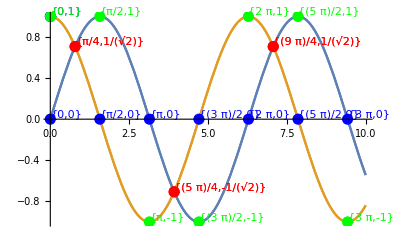

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10}]
```

If labels are appearing off the graph, you can double click the graph, and drag them back on.

If it gets too cluttered, you can filter which types of labels are shown with the Labels argument:

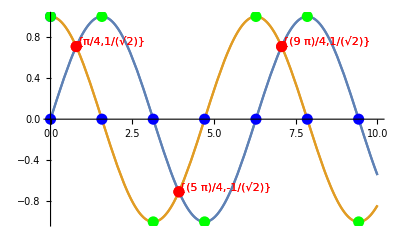

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10},Labels->Intersections]
```

Valid arguments are “Intercepts”, “Intersections”, or “Stationary” (For stationary points)

If you wish to show 2 types of labels, simply use a list.

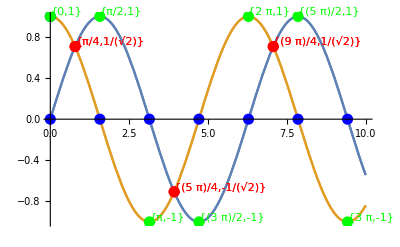

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10},Labels-> {Intersections,Stationary}]
```

### NormalLine

Finds the normal to a line at a certain point

```mathematica
NormalLine[(x+2)^2-2,x,-1]
```

1/2 (-3-x)

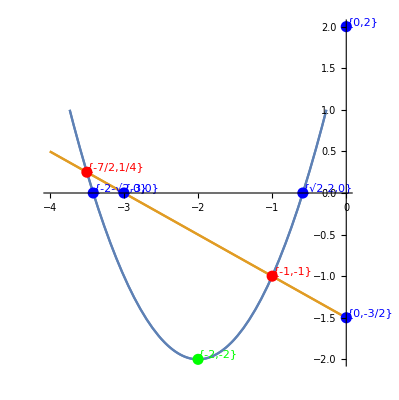

```mathematica
DetailedPlot[{(x+2)^2-2,1/2 (-3-x)},{x,-4,0},AspectRatio->Full,PlotRange-> {1,-3}]
```

### TangentLine

Finds the tangent to a curve at a certain point

```mathematica
TangentLine[expression, variable, point]
```

```mathematica
TangentLine[x^2-3x+2,x,4]
```

-14+5 x

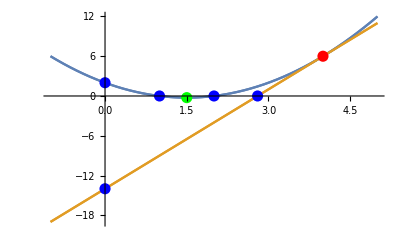

```mathematica
DetailedPlot[{x^2-3x+2,-14+5 x},{x,-1,5},Labels -> ""]
```

### Sine Rule

For side length b, and angles A and B, finds side length a.

```mathematica
SinRule[A °,{b, B °}] == a
```

```mathematica
SinRule[30°,{10,70°}]//N
```

5.32089

Remember to add ° symbol

You can also find angle A, for side lengths a,b and angle B

```mathematica
SinRuleAngle[a, {b, B °}]/°
```

```mathematica
SinRuleAngle[10,{13,60°}]/°//N
```

41.7724

Remember to divide by degrees. This is to allow for both degrees and radians to be used without two functions

### Cosine Rule

For angle A, and sides b,c, finds side a

```mathematica
CosRule[b, c, A °]
```

```mathematica
CosRule[10,20, 30°]//N
```

12.3931

For sides a,b, and c, find angle A

```mathematica
CosRuleAngle[a,b,c ]/°
```

```mathematica
CosRuleAngle[5,6,7]/Degree//N
```

44.4153

Remember to divide by degrees, this is to allow for both degrees and radians to be used in the same function.

### TurningPointForm

Converts a quadratic into turning point form.

```mathematica
TurningPointForm[x,x^2+16x+9]
```

-55+(8+x)^2

Don’t put something that isn’t a quadratic, it will make me very sad :(

```mathematica
TurningPointForm[x,2x+x^2]
```

-1+(1+x)^2

### SolveTriangle

This will solve for missing side lengths and angles of a triangles. At least 3 values and 1 side length is necessary to solve.
(Function is set to use degrees by default)

```mathematica
SolveTriangle[{a,b,c},{A,B,CC}]
```

a,b and c are side lengths.
A,B, and CC are angles.

(CC is used because C is a built in variable)

```mathematica
(*Sine Rule Question*)
SolveTriangle[{12,b,c},{A,59,73}]//N
```

{{A→48.,b→13.8412,c→15.442}}

```mathematica
(*Cosine Rule Question*)
SolveTriangle[{a,16,30},{60,B,CC}]//N
```

{{a→26.,B→32.2042,CC→87.7958}}

You can also use radians with the settings Degrees → False

```mathematica
SolveTriangle[{a,16,30},{Pi /3,B,CC},Degrees -> False]//N
```

{{a→26.,B→0.56207,CC→1.53233}}

The setting Area → True will output the area of the triangle.(You will still need placeholder symbols in place of unknown sides/angles)

```mathematica
SolveTriangle[{2,3,4},{a,b,c},Area->True]//N
```

{2.90474}

### FTest

This will check whether a function satisfies a list of conditions.

```mathematica
FTest[exp,conditions,variableName,functionName]
```

```mathematica
FTest[x+1,{h[2]==3,h[3]<2},x,h]
```

h[2]==3 is True
h[3]<2 is False

```mathematica
FTest[1/(x-1),{h[x]h[-x]==-h[x^2],h[x] + h[-x]==2h[x^2],h[x]^2==h[x^2]},x,h]
```

h[-x] h[x]==-h[x^2] is True
h[-x]+h[x]==2 h[x^2] is True
h[x]^2==h[x^2] is False

You also add assumptions for the test

```mathematica
FTest[Log[x],{h[a]+ h[b] ==h[a *b]},x,h,Assumptions->{a >0,b>0}]
```

h[a]+h[b]==h[a b] is True

From this point onwards, I have gotten lazy with documenting, so good luck :/

### RFTest

Like FTest, but instead checks whether different functions satisfy a condition.

```mathematica
RFTest[{12x,12x^2},g[a]==g[-a],x,g]
```

12 x DOES NOT satisfy condition
12 x^2 DOES satisfy condition

### Surdify

Replaces fractional powers with the surd equivalent. Note that some constants will still have a fractional power if they result in  real number.
Also note that you cannot put surdify directly into a plot command. You must copy paste its output, or use // Evaluate

```mathematica
g[x_]:=3(x-2)^3+2
```

```mathematica
InverseFunction[g][x]//Surdify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2+(-2+x)^(1/3)/3^(1/3)

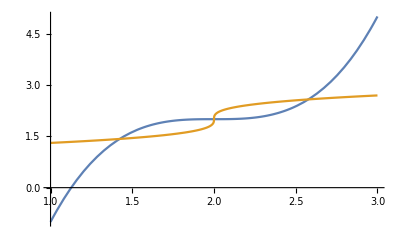

```mathematica
Plot[{g[x],InverseFunction[g][x]//Surdify//Evaluate},{x,1,3}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

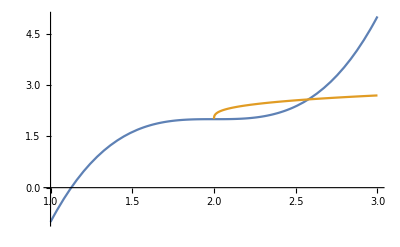

```mathematica
Plot[{g[x],InverseFunction[g][x]},{x,1,3}]
```

## Alexi’s Functions

### PolynomialDivide

Divides a polynomial

```mathematica
PolynomialDivide[numerator,denominator,variable]
PolynomialDivide[x^3+2 x^2+x,x^2,x]
```

numerator/denominator

2+1/x+x

### StationaryPoints

Finds Stationary Points of a graph

```mathematica
(*StationaryPoints[expression, variable]*)
StationaryPoints[x^3+x^2,x]
StationaryPoints[x^3,x]
StationaryPoints[1,x]
```

{{-2/3,4/27,Maximum},{0,0,Minimum}}

{{0,0,S.P.I},{0,0,S.P.I}}

{{x,1,This is a straight line}}

### FunctionInfo

Gives various information about a function
** ADD SUPPORT FOR TRIG AND PIECEWISE FUNCTIONS (Neater form / Readable S points)

```mathematica
(* FunctionInfo[function,variable] *)
FunctionInfo[x^3+2 x^2-2,x,y]
FunctionInfo[x^3-2 x^2-2,x,y]//N
FunctionInfo[1/x^2,x,y]
```

Most-Simple form: -2+x^2 (2+x)
x-intercepts: {{x→Root},{x→Root},{x→Root}}
y-intercepts: -2
1st Derivative: 4 x+3 x^2
2nd Derivative: 4+6 x
Integral: -2 x+(2 x^3)/3+x^4/4
Stationary Points: {{-4/3,-22/27,Maximum},{0,-2,Minimum}}
Domain: All Reals
Range: All Reals

Most-Simple form: -2.+(-2.+x) x^2
x-intercepts: {{x→2.3593},{x→-0.179652-0.903013 ⅈ},{x→-0.179652+0.903013 ⅈ}}
y-intercepts: -2.
1st Derivative: -4. x+3. x^2
2nd Derivative: -4.+6. x
Integral: -2. x-0.666667 x^3+0.25 x^4
Stationary Points: {{0.,-2.,Maximum},{1.33333,-3.18519,Minimum}}
Domain: All Reals
Range: All Reals

Power::infy: Infinite expression 1/0^2 encountered.

Most-Simple form: 1/x^2
x-intercepts: {}
y-intercepts: ComplexInfinity
1st Derivative: -2/x^3
2nd Derivative: 6/x^4
Integral: -1/x
Stationary Points: {}
Domain: x<0||x>0
Range: y>0

### TrigRedefine

Finds the output of the equivalent angle in another trigonometric function.

```mathematica
(* TrigRedefine[{Expression,Domain}, TargetTrigFunction, Variable] *)

TrigRedefine[{Sin[x]^2==25/169,3 π/2≤x≤2π},Cos,x]
```

{12/13}

### NewtonIterative

```mathematica
(* NewtonIterative[expression, inital guess, num of iterations, variable] *)
NewtonIterative[x^3-2,1,2,x]
```

1

4/3

91/72

### QuickTransformMatrix

Provides a standard transformation matrix (without fucking around with Mathematica and trying to click those annoying little boxes and ctrl enter combos.) for routine matrix transformation questions. The last argument can be omitted to get the final result of the matrix, or Hold can be entered to just get the matrix.

```mathematica
(* QuickTransformMatrix[a,b,c,d,x,y,h,k,Hold(optional)] *)

QuickTransformMatrix[a,0,0,b,x,y,c,d,Hold]
```

(a | 0
0 | b).(x
y)+(c
d)

```mathematica
QuickTransformMatrix[a,0,0,b,x,y,c,d]
```

{{c+a x},{d+b y}}

### InverseFunctionButBetter

The build in InverseFunction[] command does some weird stuff in an attempt to be smart. This gives you all possible Inverses of a given rule, from which you can determine the proper one yourself. 

** FUTURE ADDITION: ENTER POINT TO AUTO CHOOSE INVERSE

```mathematica
(* InverseFunctionButBetter[expression, x, y] *)
InverseFunctionButBetter[x^2,x,y]
```

{{y→-√x},{y→√x}}

DOES NOT WORK FOR COMPLEXES - FUTRE: add imaginary functionality

```mathematica
InverseFunctionButBetter[Log[x],x,y]
```

{{y→ⅇ^x}}